# DS Rate Study

## Setup: The Rate, the Delay and the Mass Distribution

## Star Formation Rate

It is logic to assume that BH merges are proportional to the Star Formation Rate (SFR). We use the Mandau function ψ that is in M_⊙Mpc^-3 yr^-1

```mathematica
ψ[z_]:=0.015*(1+z)^2.7/(1+((1+z)/2.9)^5.6)
```

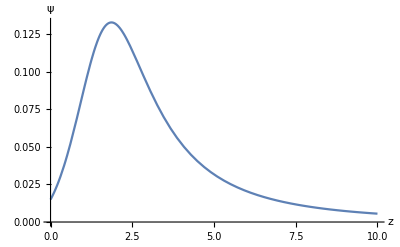

```mathematica
Plot[ψ[z],{z,0,10},AspectRatio->1/GoldenRatio,AxesLabel->{z,ψ}]
```

## Delay Function

Now that we have a SFR, we need to wait the natural life of the star in order to have some BBH. This is the ‘delay’. The delay can be modeled by an exponential decay but, for low probability, we can use 1/t as a good approximation. This t must be greater than the life of the star so t>tmin. In principle we have to take into account also the merging time for which we can not detect the  merging i.e. low and very low frequency but, since this lapse of time is negligible compared to the stellar life time,  we will ignore that .

```mathematica
EE[z_]:=(Ωm*(1+z)^3+Ωr*(1+z)^4+Ωk*(1+z)^2+Ωl)^(1/2)
```

## GW Rate

Now we can compute the GW rate. We need a prescription for t(z) in order to have an integral over z.

```mathematica
(*RGW[z_]=μ*Integrate[-ψ[x]*1/teff*tH/((1+x)EE[x]),{x,z,+∞}] *) (*This is ok but is slow. A faster version below*)
```

```mathematica
(*RGW[from_]:=(int=μ*NIntegrate[-ψ[x]*1/teff*tH/((1+x)EE[x]),x];
Limit[int,x->+∞]-Limit[int,x->from])*)
```

### Set the Cosmology

```mathematica
H0=70
```

70

```mathematica
tH=1000./H0
```

14.2857

```mathematica
Ωk=0;
```

```mathematica
Ωr=0.00008
```

0.00008

```mathematica
Ωm=0.3
```

0.3

```mathematica
Ωl=1-Ωm-Ωr
```

0.69992

### Evaluating the GW Rate & the Normalization

```mathematica
teff=1
```

1

```mathematica
cosmictime[z_]:=NIntegrate[tH/((1+x)*EE[x]),{x,z,+∞}]
```

```mathematica
cosmicdelay[z_]:=NIntegrate[tH/((1+x)*EE[x]),{x,z,+∞}]
```

```mathematica
zoft[t_]:=InverseFunction[cosmictime][t]
```

```mathematica
zoft[0.1]
```

29.9249

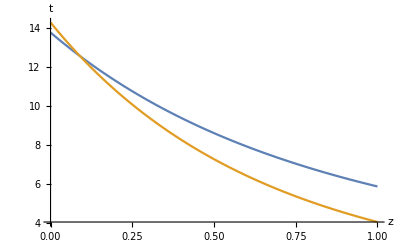

```mathematica
Plot[{cosmictime[z],tH/((1+z)*EE[z])},{z,0,1},AspectRatio->1/GoldenRatio,AxesLabel->{z,t}]
```

```mathematica
μ=25/NIntegrate[-ψ[x]*1/cosmictime[0]*tH/((1+x)EE[x]),{x,0,∞},WorkingPrecision->MachinePrecision]
```

-426.616

```mathematica
RGW[z_]:=μ*NIntegrate[-ψ[x]*1/cosmictime[z] *tH/((1+x)EE[x]),{x,z,∞},WorkingPrecision->MachinePrecision]
```

```mathematica
RGW[0]
```

25.

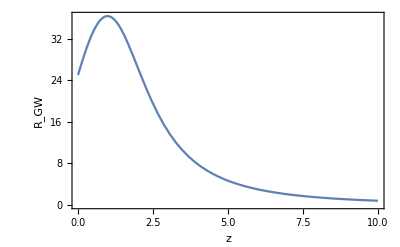

```mathematica
Plot[{RGW[z]},{z,0,10},AspectRatio->1/GoldenRatio,AxesLabel->{z,Subscript[R, GW]},Frame->{True,True,False,False},FrameStyle->Gray]
```